```mathematica
trikotnik=Trikotnik[{0,0},{5,1},{7,4}]
```

Trikotnik[{0,0},{5,1},{7,4}]

```mathematica
{Daljica[{0,0},{5,1}], Daljica[{5,1},{7,4}], Daljica[{7,4},{0,0}]}
```

{Daljica[{0,0},{5,1}],Daljica[{5,1},{7,4}],Daljica[{7,4},{0,0}]}

```mathematica
Stranice[Trikotnik[AA_,BB_,CC_]]:=
{Daljica[AA, BB], Daljica[BB, CC], Daljica[CC, AA]}
```

```mathematica
Stranice{trikotnik}
```

{Stranice Trikotnik[{0,0},{5,1},{7,4}]}

```mathematica
Koti[Trikotnik[AA_, BB_, CC_]]:={Kot[CC, AA, BB], Kot[AA, BB, CC], Kot[BB, CC, AA]}
Koti[trikotnik]/Degree//N
```

{18.4349,135.,26.5651}

```mathematica
Kot[AA_, BB_, CC_]=ArcCos[(AA-BB).(CC-BB)/(Norm[AA-BB]Norm[CC-BB])]
```

ArcCos[((AA-BB).(-BB+CC))/(Norm[AA-BB] Norm[-BB+CC])]

```mathematica
Trikotnik[{0,0},{5,1},{7,4}]
```

Trikotnik[{0,0},{5,1},{7,4}]

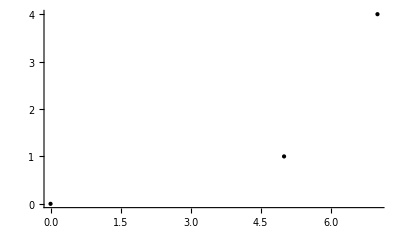

```mathematica
Graphics[{Point[{0,0}],Point[{5,1}],Point[{7,4}]}, Axes->True]
```

```mathematica
SlikaOglisc[Trikotnik[AA_,BB_,CC_]]:={Point[AA], Point[BB], Point[CC]}
```

```mathematica
Graphics[SlikaOglisc[trikotnik]]
```

-Graphics-

```mathematica
SlikaStranic[Trikotnik[AA_,BB_,CC_]]:=
{Line[{AA, BB}], Line[{BB, CC}], Line[{CC, AA}]}
```

```mathematica
NarisiTrikotnik[trikotnik_]:=
Graphics[SlikaOglisc[trikotnik], SlikaStranic[trikotnik], Axes->True]
```

```mathematica
NarisiTrikotnik[trikotnik]
```

### Naloga 1

```mathematica
ClearAll
```

ClearAll

```mathematica
trikotnik =Trikotnik[{0,0}, {5,1}, {7,4}]

Stranice[Trikotnik[AA_, BB_, CC_]] := {Daljica[AA, BB], Daljica[BB, CC], Daljica[CC, AA]}

Koti[Trikotnik[AA_, BB_, CC_]] := {Kot[CC, AA, BB],Kot[AA, BB, CC],Kot[BB, CC, AA]}

SlikaOglisc[Trikotnik[AA_, BB_, CC_]]:={Point[AA], Point[BB], Point[CC]}

SlikaStranic[Trikotnik[AA_, BB_, CC_]]:={Line[{AA, BB}], Line[{BB, CC}], Line[{CC, AA}] }

NarisiTrikotnik[t_Trikotnik]:=Graphics[{SlikaOglisc[t], SlikaStranic[t]}, AspectRatio->Automatic]
```

Trikotnik[{0,0},{5,1},{7,4}]

```mathematica
Stranice[trikotnik]
```

{Daljica[{0,0},{5,1}],Daljica[{5,1},{7,4}],Daljica[{7,4},{0,0}]}

```mathematica
Koti[trikotnik]
```

{Kot[{7,4},{0,0},{5,1}],Kot[{0,0},{5,1},{7,4}],Kot[{5,1},{7,4},{0,0}]}

```mathematica
SlikaOglisc[trikotnik]
```

{Point[{0,0}],Point[{5,1}],Point[{7,4}]}

```mathematica
SlikaStranic[trikotnik]
```

{Line[{{0,0},{5,1}}],Line[{{5,1},{7,4}}],Line[{{7,4},{0,0}}]}

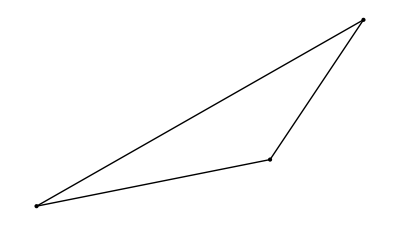

```mathematica
NarisiTrikotnik[trikotnik]
```

### Naloga 2

## 1.

```mathematica
Dolzina[Daljica[AA_, BB_]]:=Norm[BB-AA]
```

```mathematica
v={1, 2}
```

{1,2}

```mathematica
Sqrt[v.v]
```

√5

```mathematica
Norm[v]
```

√5

```mathematica
Normalize[v]
```

{1/(√5),2/(√5)}

```mathematica
v/Sqrt[v.v]
```

```mathematica
{1/(√5),2/(√5)}
```

```mathematica
Norm[{2, 3, 4}]
```

√29

```mathematica
{1, 2, 3}.{4, 5, 6}
```

32

## 2.

```mathematica
ClearAll[Kot]
```

```mathematica
VelikostKota[Kot[AA_, BB_, CC_]]:=ArcCos[(AA-BB).(CC-BB)/(Norm[AA-BB]Norm[CC-BB])]
```

```mathematica
koti=Koti[trikotnik]
```

{Kot[{7,4},{0,0},{5,1}],Kot[{0,0},{5,1},{7,4}],Kot[{5,1},{7,4},{0,0}]}

```mathematica
alfa=First[koti]
```

Kot[{7,4},{0,0},{5,1}]

```mathematica
VelikostKota[alfa]
```

ArcCos[3/(√10)]

```mathematica
FullSimplify [VelikostKota[alfa]]
```

ArcCos[3/(√10)]

## 3.

```mathematica
VektorSimetraleKota[Kot[AA_,BB_,CC_],dol_]:=
```